```mathematica
Model of a cooler
Lihong Ao
2019271014
SZU,physics
```

```mathematica
(∂ρ)/(∂t)+∇(ρ v^(->))=Subscript[S, m]
(∂(ρ v^(->)))/(∂t)+∇(ρ v^(->)v^(->))=ρ F^(->)-∇p+∇(μ(∇v^(->)+∇(v^(->))^T-2/3∇v^(->) I))+Subscript[S, p]
(∂(ρ U+(ρ (v^(->))^2)/2))/(∂t)+∇(ρ U+(ρ (v^(->))^2)/2)=ρ F^(->) v^(->)+∇(p^(->) v^(->))+∇(k grad T)+ρ q+Subscript[S, E]
```

```mathematica
Subscript[Tb, i](i=1,2,3……)      Subscript[Q, i] (i=1,2,3……)       Subscript[T, l](r^(->))    Subscript[T, v](r^(->))
Subscript[W, exchange]=∑_i Subscript[c, i](Subscript[Jo, i] Subscript[T, out]-Subscript[Ji, i] Subscript[T, in])          Jo=∑_i Subscript[Jo, i],Ji=∑_i Subscript[Ji, i]
Subscript[m, el,i]=Subscript[m, el0,i]+∫(Subscript[Ji, i]-Subscript[Jo, i]+Subscript[Jc, i]-Subscript[Je, i]) ⅆt=Subscript[m, el0,i]+∫Subscript[J, i] ⅆt
Subscript[W, Trise]=∫_evacham (∂(∑_i Subscript[c, i] Subscript[m, el,i] Subscript[T, l]))/(∂t)ⅆ r^(->)=∑_i ∫_evacham (∂(Subscript[c, i] Subscript[m, el,i] Subscript[T, l]))/(∂t)ⅆ r^(->)
(∂(Subscript[c, i] Subscript[m, el,i] Subscript[T, l]))/(∂t)=(∂(Subscript[c, i](Subscript[m, el0,i]+∫Subscript[J, i] ⅆt)Subscript[T, l]))/(∂t)=Subscript[J, i] Subscript[c, i] Subscript[T, l]+(Subscript[m, el0,i]+∫Subscript[J, i] ⅆt)(∂(Subscript[c, i] Subscript[T, l]))/(∂t)
Subscript[W, Trise]=∑_i ∫_evacham (Subscript[J, i] Subscript[c, i] Subscript[T, l]+(Subscript[m, el0,i]+∫Subscript[J, i] ⅆt)(∂(Subscript[c, i] Subscript[T, l]))/(∂t))ⅆ r^(->)
Subscript[Je, i]=Subscript[Je, i](Subscript[T, l],Subscript[T, v],p)
Subscript[𝒥e, i]=Subscript[Je, i](Subscript[T, l],Subscript[T, v],p)Subscript[Q, i],Subscript[𝒥c, i]=Subscript[Jc, i](Subscript[T, l],Subscript[T, v],Subscript[T, w],p)Subscript[Q, i]=Subscript[Jcs, i](Subscript[T, l],Subscript[T, v],p)Subscript[Q, i]+Subscript[Jcw, i](Subscript[T, w],p)Subscript[Q, i]
Subscript[W, output]=∑_i Subscript[Jcw, i] Subscript[Q, i]
W=Subscript[W, Trise]+Subscript[W, exchange]+Subscript[W, output]=∑_i ∫_evacham (Subscript[J, i] Subscript[c, i] Subscript[T, l]+(Subscript[m, el0,i]+∫Subscript[J, i] ⅆt)(∂(Subscript[c, i] Subscript[T, l]))/(∂t))ⅆ r^(->)+∑_i Subscript[c, i](Subscript[Jo, i] Subscript[T, out]-Subscript[Ji, i] Subscript[T, in])  +∑_i Subscript[Jcw, i] Subscript[Q, i]
W=∑_i ∫_evacham Subscript[J, i] Subscript[c, i] Subscript[T, l] ⅆ r^(->)+∑_i Subscript[c, i](Subscript[Jo, i] Subscript[T, out]-Subscript[Ji, i] Subscript[T, in])  +∑_i Subscript[Jcw, i] Subscript[Q, i]
p=p(Subscript[m, v])=Subscript[p, 0]+Subscript[p, 1](Subscript[m, v])
->p=Subscript[p, 0]+∫(∂p)/(∂t)ⅆt=Subscript[p, 0]+∫(∂p)/(∂Subscript[m, v])(∂Subscript[m, v])/(∂t)ⅆt=Subscript[p, 0]+∫(∂p)/(∂Subscript[m, v])(∂Subscript[m, v])/(∂t)ⅆt=Subscript[p, 0]+∫(∂p)/(∂Subscript[m, v])(Subscript[Je, i]-Subscript[Jc, i])ⅆt
p=Subscript[p, 0]+∫(∂p)/(∂Subscript[m, v])(Subscript[Je, i](Subscript[T, l],Subscript[T, v],p)-Subscript[Jc, i](Subscript[T, l],Subscript[T, v],Subscript[T, w],p))ⅆt
```

```mathematica
(∂Subscript[Tb, i])/(∂p)=Subscript[Q, i]/(Subscript[Tb, i] ΔV)>0
Subscript[((∂Subscript[Je, i])/(∂Subscript[T, l])), Subscript[T, v],r]>0
Subscript[((∂Subscript[Jcw, i])/(∂(Subscript[T, g]-Subscript[T, w]))), r]≈Subscript[((∂Subscript[Jcw, i])/(∂(Subscript[Tb, i]-Subscript[T, w]))), r]>0
(∂p)/(∂Subscript[T, g])≈(∂p)/(∂Subscript[T, l])>0
```

```mathematica
Subscript[cv, l]=1000*Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\Cv_l(T).xlsx";
Subscript[cv, g]=1000*Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\Cv_g(T).xlsx";
Subscript[cp, l]=1000*Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\Cv_l(T).xlsx";
Subscript[cp, g]=1000*Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\Cp_g(T).xlsx";
Subscript[ρ, l]=Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\density_l(T).xlsx";
Subscript[ρ, g]=Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\density_g(T).xlsx";
Subscript[ν, l]=Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\vis_l(T).xlsx";
Subscript[ν, g]=Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\vis_g(T).xlsx";
Subscript[k, l]=Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\k_l(T).xlsx";
Subscript[k, g]=Flatten@Import@"C:\\Users\\Teacher Computerium\\Pictures\\制冷剂\\氢氟烃\\r134a\\k_g(T).xlsx";
Subscript[μ, l]=Subscript[ν, l] Subscript[ρ, l];Subscript[μ, g]=Subscript[ν, g] Subscript[ρ, g];
```

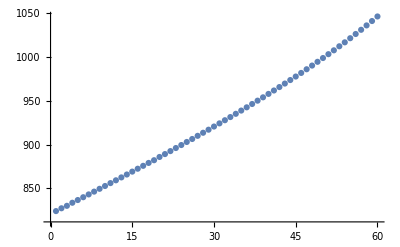

```mathematica
ListPlot@Subscript[cv, g]
```

```mathematica
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cv, l])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cv, g])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cp, l])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cp, g])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[ρ, l])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[ρ, g])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[μ, l])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[μ, g])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[k, l])^2),{a,b,d}][[2]]
Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[k, g])^2),{a,b,d}][[2]]
```

{a→0.00998724,b→0.729302,d→887.653}

{a→0.0104424,b→2.51979,d→767.356}

{a→0.00998724,b→0.729302,d→887.653}

{a→0.278586,b→-13.3979,d→1209.48}

{a→-0.0287485,b→-1.95266,d→1272.23}

{a→0.0279754,b→-0.801797,d→35.8779}

{a→7.84546×10^-9,b→-2.72109×10^-6,d→0.000257994}

{a→7.89604×10^-10,b→-1.38482×10^-8,d→0.0000115746}

{a→-2.96314×10^-7,b→-0.00040369,d→0.0913559}

{a→3.66153×10^-6,b→-0.000247088,d→0.0198737}

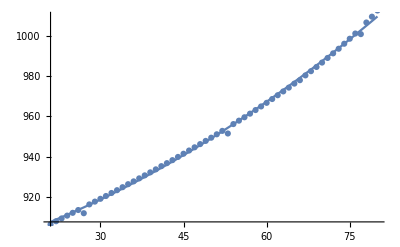

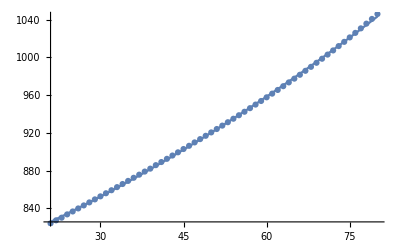

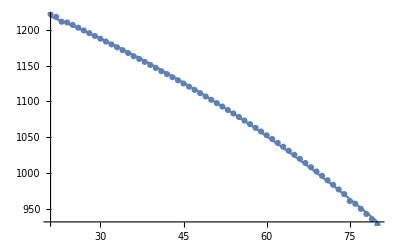

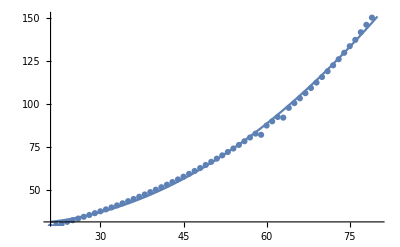

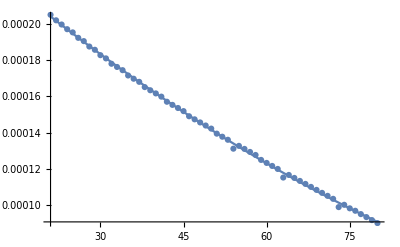

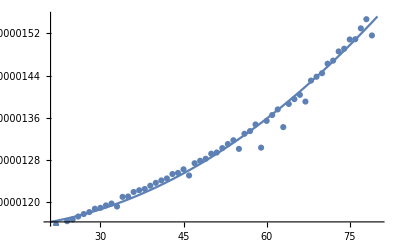

-Graphics-

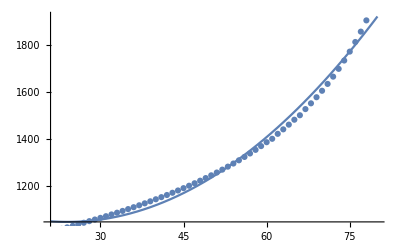

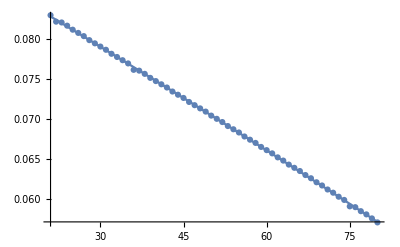

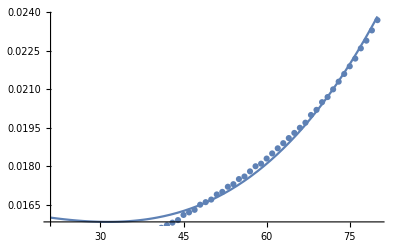

```mathematica
sol1=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cv, l])^2),{a,b,d}][[2]];
cvl[T_]:=(a/.sol1)T^2+(b/.sol1) T+d/.sol1;
sol2=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cv, g])^2),{a,b,d}][[2]];
cvg[T_]:=(a/.sol2)T^2+(b/.sol2) T+d/.sol2;
sol3=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[ρ, l])^2),{a,b,d}][[2]];
ρl[T_]:=(a/.sol3)T^2+(b/.sol3) T+d/.sol3;
sol4=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[ρ, g])^2),{a,b,d}][[2]];
ρg[T_]:=(a/.sol4)T^2+(b/.sol4) T+d/.sol4;
sol5=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[μ, l])^2),{a,b,d}][[2]];
μl[T_]:=(a/.sol5)T^2+(b/.sol5) T+d/.sol5;
sol6=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[μ, g])^2),{a,b,d}][[2]];
μg[T_]:=(a/.sol6)T^2+(b/.sol6) T+d/.sol6;
sol7=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cp, l])^2),{a,b,d}][[2]];
cpl[T_]:=(a/.sol7)T^2+(b/.sol7) T+d/.sol7;
sol8=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[cp, g])^2),{a,b,d}][[2]];
cpg[T_]:=(a/.sol8)T^2+(b/.sol8) T+d/.sol8;
sol9=Minimize[Total@((Table[a T^2+b T+d,{T,21,80}]-Subscript[k, l])^2),{a,b,d}][[2]];
kl[T_]:=(a/.sol9)T^2+(b/.sol9) T+d/.sol9;
sol10=Minimize[Total@((Table[e T^3+a T^2+b T+d,{T,21,80}]-Subscript[k, g])^2),{e,a,b,d}][[2]];
kg[T_]:=(e/.sol10)T^3+(a/.sol10)T^2+(b/.sol10) T+d/.sol10;
Show[Plot[cvl[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[cv, l]}]]
Show[Plot[cvg[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[cv, g]}]]
Show[Plot[ρl[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[ρ, l]}]]
Show[Plot[ρg[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[ρ, g]}]]
Show[Plot[μl[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[μ, l]}]]
Show[Plot[μg[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[μ, g]}]]
Show[Plot[cpl[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[cp, l]}]]
Show[Plot[cpg[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[cp, g]}]]
Show[Plot[kl[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[k, l]}]]
Show[Plot[kg[T],{T,21,80}],ListPlot[Transpose@{Table[T,{T,21,80}],Subscript[k, g]}]]
```

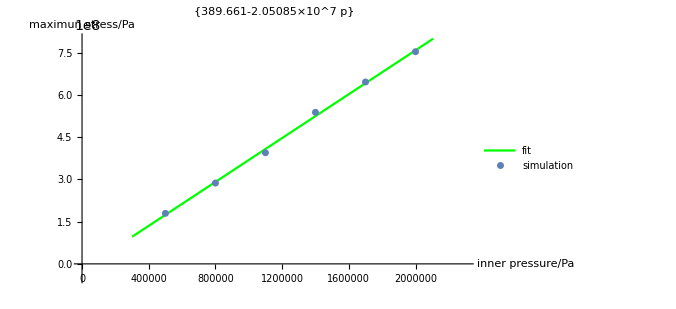

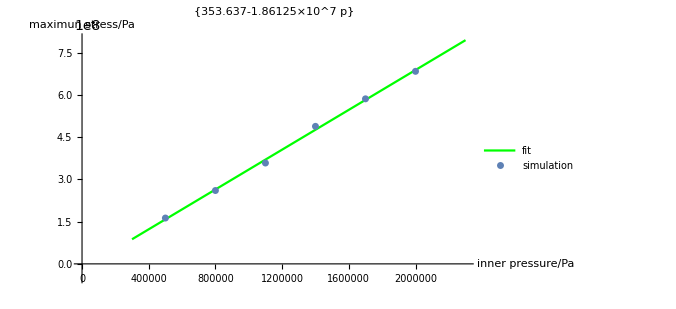

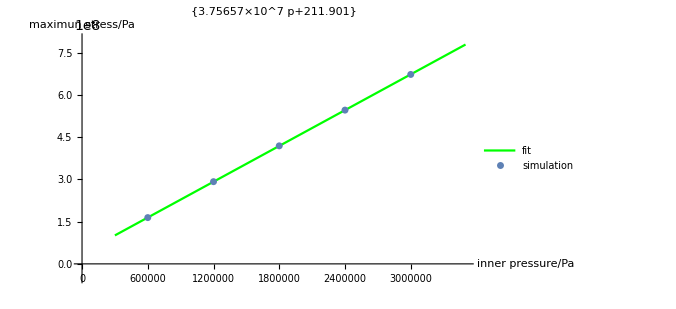

```mathematica
Clear["Global`*",Subscript]
innerpress=Table[5*10^5+3*10^5 i,{i,0,5}];
innerpress2=Table[6*10^5 i,{i,1,5}];
stressmax1={179449003.6179364,287118404.35077441,394787807.98869574,538347008.36271048,646016414.23493993,753685815.41975868};
stressmax2={162859345.57303667,260574955.54033333,358290564.70757037,488578047.64783865,586293643.49561846,684009251.41486549};
stressmax3={164372890.162954,292042103.38334519,419299789.04172248,546245929.29158044,672972627.285513};
power=1;
solp1=Minimize[Total@((Table[Sum[Subscript[a, i] p^i,{i,0,power}],{p,innerpress}]-stressmax1)^2),Table[Subscript[a, i],{i,0,power}]][[2]];
solp2=Minimize[Total@((Table[Sum[Subscript[b, i] p^i,{i,0,power}],{p,innerpress}]-stressmax2)^2),Table[Subscript[b, i],{i,0,power}]][[2]];
solp3=Minimize[Total@((Table[Sum[Subscript[c, i] p^i,{i,0,power}],{p,innerpress2}]-stressmax3)^2),Table[Subscript[c, i],{i,0,power}]][[2]];
stressmax1fit[p_]:=Sum[(Subscript[a, i]/.solp1)p^i,{i,0,power}];
stressmax2fit[p_]:=Sum[(Subscript[b, i]/.solp2)p^i,{i,0,power}];
stressmax3fit[p_]:=Sum[(Subscript[c, i]/.solp3)p^i,{i,0,power}];
Show[Plot[stressmax1fit[p],{p,0.3*10^6,2.3*10^6},PlotStyle->Green,PlotRange->{{0,2.3*10^6},{-5*10^7,8*10^8}},AxesLabel->{"inner pressure/Pa","maximun stress/Pa"},PlotLabel->{(Subscript[a, 0]/.solp1) p+(Subscript[a, 1]/.solp1)},PlotLegends->{fit},ImageSize->500],ListPlot[Transpose@{innerpress,stressmax1},PlotStyle->PointSize[.01],PlotLegends->{simulation}]]
Show[Plot[stressmax2fit[p],{p,0.3*10^6,2.3*10^6},PlotStyle->Green,PlotRange->{{0,2.3*10^6},{-5*10^7,8*10^8}},AxesLabel->{"inner pressure/Pa","maximun stress/Pa"},PlotLabel->{(Subscript[b, 0]/.solp2) p+(Subscript[b, 1]/.solp2)},PlotLegends->{fit},ImageSize->500],ListPlot[Transpose@{innerpress,stressmax2},PlotStyle->PointSize[.01],PlotLegends->{simulation}]]
Show[Plot[stressmax3fit[p],{p,0.3*10^6,3.5*10^6},PlotStyle->Green,PlotRange->{{0,3.5*10^6},{-5*10^7,8*10^8}},AxesLabel->{"inner pressure/Pa","maximun stress/Pa"},PlotLabel->{(Subscript[c, 0]/.solp3) p+(Subscript[c, 1]/.solp3)},PlotLegends->{fit},ImageSize->500],ListPlot[Transpose@{innerpress2,stressmax3},PlotStyle->PointSize[.01],PlotLegends->{simulation}]]
```

```mathematica
Grid[{{"surge bin for cluster"},Flatten@{"inner pressure/Pa",innerpress},Flatten@{"maximum stress/Pa",stressmax1}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.25],All}},Background->{None,{GrayLevel[0.7],{White}}}]
Grid[{{"surge bin for single machine"},Flatten@{"inner pressure/Pa",innerpress},Flatten@{"maximum stress/Pa",stressmax2}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.265],All}},Background->{None,{GrayLevel[0.7],{White}}}]
Grid[{{" heat dissipation main part(rack mounted)"},Flatten@{"inner pressure/Pa",innerpress2},Flatten@{"maximum stress/Pa",stressmax3}},Alignment->Left,Frame->All,ItemSize->{{Scaled[.3],All}},Background->{None,{GrayLevel[0.7],{White}}}]
```

surge bin for cluster |  |  |  |  |  | 
inner pressure/Pa | 500000 | 800000 | 1100000 | 1400000 | 1700000 | 2000000
maximum stress/Pa | 1.79449×10^8 | 2.87118×10^8 | 3.94788×10^8 | 5.38347×10^8 | 6.46016×10^8 | 7.53686×10^8

surge bin for single machine |  |  |  |  |  | 
inner pressure/Pa | 500000 | 800000 | 1100000 | 1400000 | 1700000 | 2000000
maximum stress/Pa | 1.62859×10^8 | 2.60575×10^8 | 3.58291×10^8 | 4.88578×10^8 | 5.86294×10^8 | 6.84009×10^8

heat dissipation main part(rack mounted) |  |  |  |  | 
inner pressure/Pa | 600000 | 1200000 | 1800000 | 2400000 | 3000000
maximum stress/Pa | 1.64373×10^8 | 2.92042×10^8 | 4.193×10^8 | 5.46246×10^8 | 6.72973×10^8

```mathematica
Clear["Global`*"]
```